```mathematica
Exit
```

```mathematica
(* center at origin to corner at origin *)
rotL[data_]:=RotateLeft[data, Floor@Dimensions[data][[#]]/2&/@Range[Length@Dimensions[data]]];
(* corner at orign to center at origin *)
rotR[data_]:=RotateRight[data, Floor@Dimensions[data][[#]]/2&/@Range[Length@Dimensions[data]]];
(* {x,y} means {x,y}/λ, {kx,ky} means {kx,ky}/k *)
(* rotR[F[aList,xList,kList]]==F[rotR[aList],rotR[xList],rotR[kList]] *)
(* rotR[F[rotL[aList],xList,kList]]==F[aList,rotR[xList],rotR[kList]] *)
(*FFT[f_]:=rotR[Fourier[rotL[f],FourierParameters->{-1,-1}]];
iFFT[f_]:=rotR[Fourier[rotL[f],FourierParameters->-{-1,-1}]];*)
FFT[f_] :=rotR[Fourier[f, FourierParameters->{1, -1}]];
iFFT[f_]:=InverseFourier[rotL[f], FourierParameters->{1, -1}];
```

```mathematica
p=0.31 2;size=32p;λ=0.810;k0=2π/λ ;
{nx,ny}={Floor[size/p],Floor[size/p]};
{lx,ly}={nx*p,ny*p};
{dx,dy}={p,p};
{dkx, dky}=2π*{1/(p*nx),1/(p*ny)};
padRatio=10;(*PadRatio=15;*)
{padx,pady} = (padRatio-1)/2*{nx,ny};
Echo[{nx p,ny p},"Sample size in um: "];
Echo[{nx,ny},"Sample size in pixel: "];
θx=10Degree;θy=10Degree;
k0=(2π)/λ;
f=150;
T2=({{-1, 1, 1, 1, 1, 1, 0, 0, 0}, {1, -1, 1, 1, 1, 0, 1, 0, 0}, {1, 1, -1, 1, 0, 0, 0, 0, 1}, {1, 1, 1, -1, 1, 0, 0, 1, 0}, {1, 1, 0, 1, -1, -1, -1, -1, -1}, {1, 0, 0, 0, -1, -ⅈ, 1, 1, ⅈ}, {0, 1, 0, 0, -1, 1, -1, -1, 1}, {0, 0, 0, 1, -1, 1, -1, -1, 1}, {0, 0, 1, 0, -1, ⅈ, 1, 1, -ⅈ}});
```

Sample size in um:   {19.84,19.84}

Sample size in pixel:   {32,32}

```mathematica
(*centerRange[n_,d_]:=Table[(i-n/2-.5)*d,{i,n}];
{y,x}=centerRange@@#&/@{{ny, dy}, {nx,dx}};
ellipticalMask=Map[If[#<(lx ly)/4,1,0]&,Outer[Plus,y^2,x^2],{2}];
H[A_,z_] := Module[{nx, ny, kx, ky},
{nx, ny}=Dimensions[A][[#]]&/@{2,1};
{kx,ky}=centerRange[#, (2π)/(p #)]&/@{nx,ny};
Exp[ⅈ *z*√(k0^2 - Outer[Plus,kx^2,ky^2])]
]; 
forwardPropagate[A_,z_]:=iFFT[FFT[A] *H[A,z]];

eFocus = Exp[-ⅈ*k0*(√(Outer[Plus,y^2,x^2]+f^2)-f)];
A= eFocus*ellipticalMask//ArrayPad[#,100]&;
{A//MatrixPlot[# ]&, 
Abs[forwardPropagate[A,f]]^2//ArrayPlot[#,PlotTheme->"Detailed"]&}*)
```

META DESIGN WITH LENS FOCUSING

```mathematica
centerRange[n_,d_]:=Table[(i-n/2-.5)*d,{i,n}];
k = k0*Sin/@({{{-θx, -θy}, {0, -θy}, {θx, -θy}}, {{-θx, 0}, {0, 0}, {θx, 0}}, {{-θx, θy}, {0, θy}, {θx, θy}}})//N;
r0 = -p*({{{-nx, -ny}, {0, -ny}, {nx, -ny}}, {{-nx, 0}, {0, 0}, {nx, 0}}, {{-nx, ny}, {0, ny}, {nx, ny}}})//N;
{kx,ky}=Flatten@Part[k, ;;,;;,#]&/@{1,2};
{x0,y0}=Flatten@Part[r0, ;;,;;,#]&/@{1,2};
{fx,fy}={kx/(√(k0^2-kx^2)),ky/(√(k0^2-ky^2))}*f;
{x,y}=centerRange@@#&/@{{nx, dx}, {ny,dy}};
ellipticalMask=Map[If[#<(lx ly)/4,1,0]&,Outer[Plus,y^2,x^2],{2}];
globalEllipticalMask := KroneckerProduct[({{1, 1, 1}, {1, 1, 1}, {1, 1, 1}}), ellipticalMask];
(* Method 1: shift the center of the lens by fx,fy;
	but the lens interference might not be perfect *)
(*eLocalLens[i_] := 
If[i!=0,
Sum[T2[[j]][[i]]* Exp[-ⅈ*k0*(√(Outer[Plus,(y-y0[[i]]-fy[[j]])^2,(x-x0[[i]]-fx[[j]])^2]+f^2)-f)]*ellipticalMask,{j,9}]
,ConstantArray[0,{nx,ny}]];*)

(* Method 2: focus at the center and deflect the beam, but the focusing plane is not parallel with the optical axis. *)
eLocalLens[i_] := 
If[i!=0,
Sum[T2[[j]][[i]]* 
Exp[-ⅈ k0 √(Outer[Plus,(y-y0[[i]])^2,(x-x0[[i]])^2]+(f^2+fy[[j]]^2+fx[[j]]^2))
(*+ⅈ k0 √(f^2+(fy[[j]]-y0[[i]])^2+(fx[[j]]-x0[[i]])^2)*)
+ⅈ Outer[Plus,ky[[j]](y-y0[[i]]),kx[[j]](x-x0[[i]])]]
*ellipticalMask,{j,9}]
,ConstantArray[0,{nx,ny}]];

eGlobalLens[arg_]:= ArrayFlatten[Map[eLocalLens,Map[If[#!=0, 1,0]&, arg,{2}]*({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}),{2}]];
eGlobalInput[arg_]:=ArrayFlatten[Map[#*ConstantArray[1,{ny,nx}]&,arg,{2}]];
meta=eGlobalLens[({{1, 1, 1}, {1, 1, 1}, {1, 1, 1}})];
H[A_,z_,{dx_,dy_}] := Module[{nx, ny, kx, ky},
{nx, ny}=Dimensions[A][[#]]&/@{2,1};
{kx,ky}=centerRange@@#&/@{{nx, (2π)/(dx nx)},{ny,(2π)/(dy ny)}};
Exp[ⅈ *z*√(k0^2 - Outer[Plus,kx^2,ky^2])]
]; 
forwardPropagate[A_,z_,{dx_, dy_}]:=iFFT[FFT[A] *H[A,z,{dx, dy}]];
farField[arg_]:=forwardPropagate[ArrayPad[eGlobalInput[arg]*meta,{{pady},{padx}}],f, {p, p}]//Abs[#]^2&;
```

```mathematica
Echo["LocalLens"];
MatrixPlot@* eLocalLens/@Range[9]//ArrayReshape[#,{3,3}]&//GraphicsGrid[#,ImageSize->Medium]&//Rasterize

Echo["GlobalLens"];
MatrixPlot@*eGlobalLens/@(IdentityMatrix[9]//ArrayReshape[#,{9,3,3}]&)//ArrayReshape[#,{3,3}]&//GraphicsGrid[#,ImageSize->Medium]&//Rasterize

Echo["GlobalInput"];
ArrayPlot@*eGlobalInput/@(IdentityMatrix[9]//ArrayReshape[#,{9,3,3}]&)//ArrayReshape[#,{3,3}]&//GraphicsGrid[#,ImageSize->Medium]&//Rasterize

Echo["FarField"];ArrayPlot@*farField/@(IdentityMatrix[9]//ArrayReshape[#,{9,3,3}]&)//ArrayReshape[#,{3,3}]&//GraphicsGrid[#,ImageSize->Medium]&//Rasterize
```

LocalLens

-Graphics-

GlobalLens

-Graphics-

GlobalInput

-Graphics-

FarField

-Graphics-

```mathematica
test[f_,inputs_]:=ArrayPlot  @*f/@inputs//GraphicsGrid[{#}]&//Rasterize;

testGrover={({{-1, 1, 0}, {1, 1, 0}, {0, 0, 0}}),({{1, -1, 0}, {1, 1, 0}, {0, 0, 0}}),({{1, 1, 0}, {-1, 1, 0}, {0, 0, 0}}),({{1, 1, 0}, {1, -1, 0}, {0, 0, 0}})};
testQFT={({{0, 0, 0}, {0, 1, 1}, {0, 1, 1}}),({{0, 0, 0}, {0, 1, -ⅈ}, {0, -1, ⅈ}}),({{0, 0, 0}, {0, 1, -1}, {0, 1, -1}}),({{0, 0, 0}, {0, 1, ⅈ}, {0, -1, -ⅈ}})};
testCNOT={({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}}),({{0, 0, 0}, {0, 0, 0}, {1, 0, 0}}),({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}}),({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}})};

Echo["Test Grover"];
(*ArrayPlot  @*farField/@testGrover//GraphicsGrid[{#}]&//Rasterize*)
test[farField,testGrover]

Echo["Test QFT"];
(*ArrayPlot  @*farField/@testQFT//GraphicsGrid[{#}]&//Rasterize*)
test[farField,testQFT]

Echo["Test CNOT"];
(*ArrayPlot  @*farField/@testCNOT//GraphicsGrid[{#}]&//Rasterize*)
test[farField,testCNOT]
```

Test Grover

-Graphics-

Test QFT

-Graphics-

Test CNOT

-Graphics-

EXPORT META DESIGN TO CSV

```mathematica
path = FileNameJoin[{DirectoryName@NotebookDirectory[],"meta-design"}]
Export[FileNameJoin[{path,"metaLensf150DeflectAmp.csv"}],Abs[meta]]
Export[FileNameJoin[{path,"metaLensf150DeflectArg.csv"}],Abs[meta]]
Export[FileNameJoin[{path,"metaLensf150Mask.csv"}],Abs[globalEllipticalMask]]
```

/home/stnav/Projects/jensen-lab-mathematica/meta-design

/home/stnav/Projects/jensen-lab-mathematica/meta-design/metaLensf150DeflectAmp.csv

/home/stnav/Projects/jensen-lab-mathematica/meta-design/metaLensf150DeflectArg.csv

/home/stnav/Projects/jensen-lab-mathematica/meta-design/metaLensf150Mask.csv

CONVERT META DESIGN TO DOUBLE SLOT PAIRS

```mathematica
convertPair[meta_] := Module[{ϕ1, ϕ2},
ϕ1 = Arg[#]+ArcCos[Abs[#]]&;
ϕ2 = Arg[#]-ArcCos[Abs[#]]&;
metaNorm:=meta/Max[Abs[meta]];
Exp[ⅈ Outer[#2[#1]&,metaNorm,({{ϕ1, ϕ2}, {ϕ2, ϕ1}})]]//Flatten[#,{{1,3},{2,4}}]&
];

metaPair=convertPair[meta]*KroneckerProduct[globalEllipticalMask,({{1, 1}, {1, 1}})];
farFieldPair[arg_]:=forwardPropagate[
ArrayPad[
KroneckerProduct[eGlobalInput[(arg)],({{1, 1}, {1, 1}})]*metaPair,
2*{{pady},{padx}}],
f,{p/2,p/2}]//Abs[#]^2&;
```

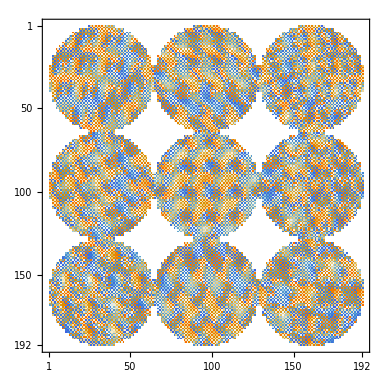

FarField

-Graphics-

```mathematica
metaPair//Arg//MatrixPlot

Echo["FarField"];
ArrayPlot@*farFieldPair/@(IdentityMatrix[9]//ArrayReshape[#,{9,3,3}]&)//ArrayReshape[#,{3,3}]&//GraphicsGrid[#,ImageSize->Medium]&//Rasterize
```

```mathematica
testGrover={({{-1, 1, 0}, {1, 1, 0}, {0, 0, 0}}),({{1, -1, 0}, {1, 1, 0}, {0, 0, 0}}),({{1, 1, 0}, {-1, 1, 0}, {0, 0, 0}}),({{1, 1, 0}, {1, -1, 0}, {0, 0, 0}})};
testQFT={({{0, 0, 0}, {0, 1, 1}, {0, 1, 1}}),({{0, 0, 0}, {0, 1, -ⅈ}, {0, -1, ⅈ}}),({{0, 0, 0}, {0, 1, -1}, {0, 1, -1}}),({{0, 0, 0}, {0, 1, ⅈ}, {0, -1, -ⅈ}})};
testCNOT={({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}}),({{0, 0, 0}, {0, 0, 0}, {1, 0, 0}}),({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}}),({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}})};

Echo["Test Grover"];ArrayPlot  @*farFieldPair/@testGrover//GraphicsGrid[{#}]&//Rasterize

Echo["Test QFT"];
ArrayPlot @*farFieldPair/@testQFT//GraphicsGrid[{#}]&//Rasterize

Echo["Test CNOT"];
ArrayPlot @*farFieldPair/@testCNOT//GraphicsGrid[{#}]&//Rasterize
```

Test Grover

-Graphics-

Test QFT

-Graphics-

Test CNOT

-Graphics-

CONVERT META DESIGN TO ARG ONLY

```mathematica
convertArg[meta_] := Module[{ϕ0},
ϕ0 = Arg[#]&;
metaNorm:=meta/Max[Abs[meta]];
Exp[ⅈ Outer[#2[#1]&,metaNorm,{{ϕ0}}]]//Flatten[#,{{1,3},{2,4}}]&
];

metaArg=convertArg[meta]*globalEllipticalMask;
farFieldArg[arg_]:=forwardPropagate[
ArrayPad[
eGlobalInput[(arg)]*metaArg,
{{pady},{padx}}],
f,{p,p}]//Abs[#]^2&;
```

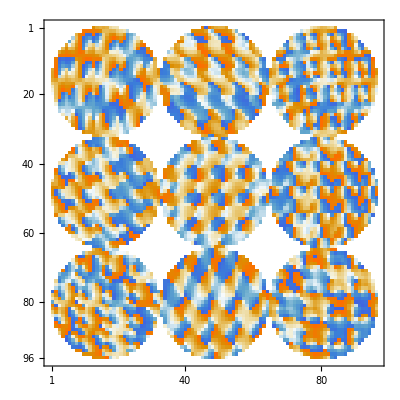

FarField

-Graphics-

```mathematica
metaArg//Arg//MatrixPlot

Echo["FarField"];
ArrayPlot@*farFieldArg/@(IdentityMatrix[9]//ArrayReshape[#,{9,3,3}]&)//ArrayReshape[#,{3,3}]&//GraphicsGrid[#,ImageSize->Medium]&//Rasterize
```

```mathematica
testGrover={({{-1, 1, 0}, {1, 1, 0}, {0, 0, 0}}),({{1, -1, 0}, {1, 1, 0}, {0, 0, 0}}),({{1, 1, 0}, {-1, 1, 0}, {0, 0, 0}}),({{1, 1, 0}, {1, -1, 0}, {0, 0, 0}})};
testQFT={({{0, 0, 0}, {0, 1, 1}, {0, 1, 1}}),({{0, 0, 0}, {0, 1, -ⅈ}, {0, -1, ⅈ}}),({{0, 0, 0}, {0, 1, -1}, {0, 1, -1}}),({{0, 0, 0}, {0, 1, ⅈ}, {0, -1, -ⅈ}})};
testCNOT={({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}}),({{0, 0, 0}, {0, 0, 0}, {1, 0, 0}}),({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}}),({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}})};

Echo["Test Grover"];ArrayPlot  @*farFieldArg/@testGrover//GraphicsGrid[{#}]&//Rasterize

Echo["Test QFT"];
ArrayPlot @*farFieldArg/@testQFT//GraphicsGrid[{#}]&//Rasterize

Echo["Test CNOT"];
ArrayPlot @*farFieldArg/@testCNOT//GraphicsGrid[{#}]&//Rasterize
```

Test Grover

-Graphics-

Test QFT

-Graphics-

Test CNOT

-Graphics-